# Lecture 6: Tutorial 1

Question: Do you approve or disapprove of the way [enter President name] is handling his job as President?

Data adapted from the Gallup Poll and compiled by Gerhard Peters

Goal: to visualize US presidential job approval rate in time.

Data science task: scrapping a Webpage, augmenting it with the Wolfram language, visualizing pre-processed data.

Plot data using directly the Dataset formalism

## Instructions

Step 1) Import data from "https://www.presidency.ucsb.edu/statistics/data/initial-presidential-job-approval-ratings”

Step 2) Take a look at the Website to understand the structure of the data. Find where the relevant data is in the dataset.

Step3) Calculate the average approval rate, make an histogram of the approval rate, and plot maximal approval rate in time, using the Dataset formalism

## Step1) Import data

```mathematica
URL["https://www.presidency.ucsb.edu/statistics/data/presidential-job-approval"]
```

URL[https://www.presidency.ucsb.edu/statistics/data/presidential-job-approval]

```mathematica
Clear[importdata]
```

```mathematica
importdata = Import["https://www.presidency.ucsb.edu/statistics/data/initial-presidential-job-approval-ratings","Data"]
```

{{{Guidebook,Category Attributes},{Data Archive,Elections},Media Archive,Presidents,Analyses,GIVE},{{Data Archive,Elections},{{Year,Interview Dates,President,% Approval,% Disapproval,% No Opinion},{{1953,Feb. 1-5,Dwight D. Eisenhower,68,7,25},{1961,Feb. 10-15,John Kennedy,72,6,22},{1969,Jan. 23-28,Richard Nixon,59,5,36},{1977,Feb. 4-7,Jimmy Carter,66,8,26},{1981,Jan. 30-Feb. 2,Ronald Reagan,51,13,36},{1989,Jan. 24-26,George Bush,51,6,43},{1993,Jan. 24-26,William J. Clinton,58,20,22},{2001,Feb. 1-4,George W. Bush,57,25,18},{2009,Jan. 21-23,Barack Obama,68,12,21},{2017,Jan. 20-29,Donald J. Trump,45,47,8},{2021,Jan. 21-Feb. 2,Joseph R. Biden, Jr.,57,37,6},{2025,Jan 21-27,Donald J. Trump,47,48,5}}}}}

## Step 2) Take a look at the Website to understand the structure of the data. Find where the relevant data is in the dataset.

Query about the data dimension :

```mathematica
Dimensions[importdata]
```

{2}

The relevant information is on the element (array) 2 :

```mathematica
importdata[[2]]
```

{{Data Archive,Elections},{{Year,Interview Dates,President,% Approval,% Disapproval,% No Opinion},{{1953,Feb. 1-5,Dwight D. Eisenhower,68,7,25},{1961,Feb. 10-15,John Kennedy,72,6,22},{1969,Jan. 23-28,Richard Nixon,59,5,36},{1977,Feb. 4-7,Jimmy Carter,66,8,26},{1981,Jan. 30-Feb. 2,Ronald Reagan,51,13,36},{1989,Jan. 24-26,George Bush,51,6,43},{1993,Jan. 24-26,William J. Clinton,58,20,22},{2001,Feb. 1-4,George W. Bush,57,25,18},{2009,Jan. 21-23,Barack Obama,68,12,21},{2017,Jan. 20-29,Donald J. Trump,45,47,8},{2021,Jan. 21-Feb. 2,Joseph R. Biden, Jr.,57,37,6},{2025,Jan 21-27,Donald J. Trump,47,48,5}}}}

Use MatrixForm to understand the matrix format :

```mathematica
MatrixForm[%]
```

(Data Archive | Elections
{Year,Interview Dates,President,% Approval,% Disapproval,% No Opinion} | {{1953,Feb. 1-5,Dwight D. Eisenhower,68,7,25},{1961,Feb. 10-15,John Kennedy,72,6,22},{1969,Jan. 23-28,Richard Nixon,59,5,36},{1977,Feb. 4-7,Jimmy Carter,66,8,26},{1981,Jan. 30-Feb. 2,Ronald Reagan,51,13,36},{1989,Jan. 24-26,George Bush,51,6,43},{1993,Jan. 24-26,William J. Clinton,58,20,22},{2001,Feb. 1-4,George W. Bush,57,25,18},{2009,Jan. 21-23,Barack Obama,68,12,21},{2017,Jan. 20-29,Donald J. Trump,45,47,8},{2021,Jan. 21-Feb. 2,Joseph R. Biden, Jr.,57,37,6},{2025,Jan 21-27,Donald J. Trump,47,48,5}})

The second element of this list (or the Row 2 in the matrix) is where the data is :

```mathematica
importdata[[2,2]]
```

{{Year,Interview Dates,President,% Approval,% Disapproval,% No Opinion},{{1953,Feb. 1-5,Dwight D. Eisenhower,68,7,25},{1961,Feb. 10-15,John Kennedy,72,6,22},{1969,Jan. 23-28,Richard Nixon,59,5,36},{1977,Feb. 4-7,Jimmy Carter,66,8,26},{1981,Jan. 30-Feb. 2,Ronald Reagan,51,13,36},{1989,Jan. 24-26,George Bush,51,6,43},{1993,Jan. 24-26,William J. Clinton,58,20,22},{2001,Feb. 1-4,George W. Bush,57,25,18},{2009,Jan. 21-23,Barack Obama,68,12,21},{2017,Jan. 20-29,Donald J. Trump,45,47,8},{2021,Jan. 21-Feb. 2,Joseph R. Biden, Jr.,57,37,6},{2025,Jan 21-27,Donald J. Trump,47,48,5}}}

The Keys are the first element of the list :

```mathematica
importdata[[2,2,1]]
```

{Year,Interview Dates,President,% Approval,% Disapproval,% No Opinion}

whereas the data is on the second

```mathematica
importdata[[2,2,2]]
```

{{1953,Feb. 1-5,Dwight D. Eisenhower,68,7,25},{1961,Feb. 10-15,John Kennedy,72,6,22},{1969,Jan. 23-28,Richard Nixon,59,5,36},{1977,Feb. 4-7,Jimmy Carter,66,8,26},{1981,Jan. 30-Feb. 2,Ronald Reagan,51,13,36},{1989,Jan. 24-26,George Bush,51,6,43},{1993,Jan. 24-26,William J. Clinton,58,20,22},{2001,Feb. 1-4,George W. Bush,57,25,18},{2009,Jan. 21-23,Barack Obama,68,12,21},{2017,Jan. 20-29,Donald J. Trump,45,47,8},{2021,Jan. 21-Feb. 2,Joseph R. Biden, Jr.,57,37,6},{2025,Jan 21-27,Donald J. Trump,47,48,5}}

```mathematica
keyset={"Year","Dates","President","Approval","Disapproval","Noopinion"}
```

{Year,Dates,President,Approval,Disapproval,Noopinion}

```mathematica
dsImportdata1 = AssociationThread[keyset->#]&/@importdata[[2,2,2]]
```

{<|Year→1953,Dates→Feb. 1-5,President→Dwight D. Eisenhower,Approval→68,Disapproval→7,Noopinion→25|>,<|Year→1961,Dates→Feb. 10-15,President→John Kennedy,Approval→72,Disapproval→6,Noopinion→22|>,<|Year→1969,Dates→Jan. 23-28,President→Richard Nixon,Approval→59,Disapproval→5,Noopinion→36|>,<|Year→1977,Dates→Feb. 4-7,President→Jimmy Carter,Approval→66,Disapproval→8,Noopinion→26|>,<|Year→1981,Dates→Jan. 30-Feb. 2,President→Ronald Reagan,Approval→51,Disapproval→13,Noopinion→36|>,<|Year→1989,Dates→Jan. 24-26,President→George Bush,Approval→51,Disapproval→6,Noopinion→43|>,<|Year→1993,Dates→Jan. 24-26,President→William J. Clinton,Approval→58,Disapproval→20,Noopinion→22|>,<|Year→2001,Dates→Feb. 1-4,President→George W. Bush,Approval→57,Disapproval→25,Noopinion→18|>,<|Year→2009,Dates→Jan. 21-23,President→Barack Obama,Approval→68,Disapproval→12,Noopinion→21|>,<|Year→2017,Dates→Jan. 20-29,President→Donald J. Trump,Approval→45,Disapproval→47,Noopinion→8|>,<|Year→2021,Dates→Jan. 21-Feb. 2,President→Joseph R. Biden, Jr.,Approval→57,Disapproval→37,Noopinion→6|>,<|Year→2025,Dates→Jan 21-27,President→Donald J. Trump,Approval→47,Disapproval→48,Noopinion→5|>}

```mathematica
aa=Dataset[%]
```

## Step3) Calculate the average approval rate, make an histogram of the approval rate, and plot maximal approval rate in time.

The rest is "simple" :)! 

Let us operate on the dataset, calculating the mean of approval:

```mathematica
aa[Mean,"Approval"]
```

233/4

```mathematica
119/2//N
```

59.5

Plotting an histogram

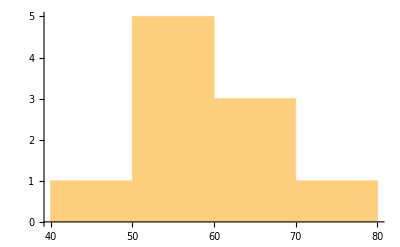

```mathematica
aa[Histogram,"Approval"]
```

```mathematica
aa[[All,"Approval"]]
```

```mathematica
Query[All, "Approval"][aa]
```

Below if we do this, the Max function will be applied separately at each value of the key - value association

```mathematica
Query[All,#[[4]]&][aa]
```

Let us create an expression that is a command (effectively behaving as a function)

```mathematica
k=Query[All,"Approval"]
```

Query[All,Approval]

```mathematica
k[aa]
```

```mathematica
k1=Query[All,#[[4]]&]
```

Query[All,#1⟦4⟧&]

```mathematica
Clear[q]
```

Here bellow a Function in the strict sense of Mathematica

```mathematica
q[f_]:=Query[All,#[[4]]&][f];
```

```mathematica
q[aa]
```

```mathematica
k1[aa]
```

```mathematica
q[aa]
```

```mathematica
Query[All,"Approval"][aa]
```

```mathematica
Query[Total,"Approval"][aa]
```

699

```mathematica
Query[Max,"Approval"][aa]
```

72

```mathematica
Query[All,"Approval"][aa]
```

```mathematica
Query[All,All, f][aa]
```

This applies separated to each element of the column "Approval"

```mathematica
Query[All, "Approval", f][aa]
```

The bellow applies for the whole "Approval" column

```mathematica
Query[f, "Approval"][aa]
```

f[{68,72,59,66,51,51,58,57,68,45}]

keeping only the year

```mathematica
a1=aa[[All, "Year"]]
```

```mathematica
a2=aa[[All, "Approval"]]
```

Plot the data :

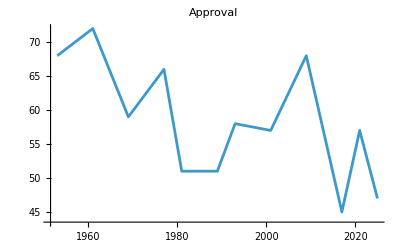

```mathematica
ListPlot[Table[{a1[[i]],a2[[i]]},{i,12}],PlotLabel->"Approval",Joined-> {True}]
```

Or simply use the syntax of Datasets :

```mathematica
ListPlot[Transpose[{Normal[aa[All,"Year"]],Normal[aa[All,"Approval"]]}],PlotLabel->"Approval",Joined-> {True}]
```

-Graphics-

More compactly :

```mathematica
ListPlot[Normal[{Normal[#Year],Normal[#Approval]}&/@aa],PlotLabel->"Approval",Joined-> {True}]
```

-Graphics-

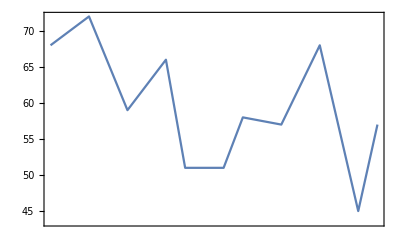

```mathematica
DateListPlot[aa[All,{"Year","Approval"}]]
```